```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/QMB.wl"]
```

## Ising

Importar eigenenergías y calcular ⟨r̃⟩:

```mathematica
data=Import["data/eigenenergies/ising/L_16_hx_1_even_parity.csv","CSV"];
{parameters,rtilde}=Transpose[{#[[1;;2]],MeanLevelSpacingRatio[#[[3;;]]]}&/@data];ClearAll[data];
```

Importar valor esperado de Haar de la pureza de Choi y calcular el promedio temporal:

```mathematica
{t0,tf}={0,49.5};
meanchoipurity=Table[
Module[{hz=i[[1]],J=i[[2]],choipurityinterpolated},
choipurityinterpolated=Interpolation[Import["data/haar_avg_choi_purity/ising/L_7/hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>".csv","CSV"][[2;;]]];
NIntegrate[choipurityinterpolated[t],{t,t0,tf}]/tf
]
,{i,parameters}];
```

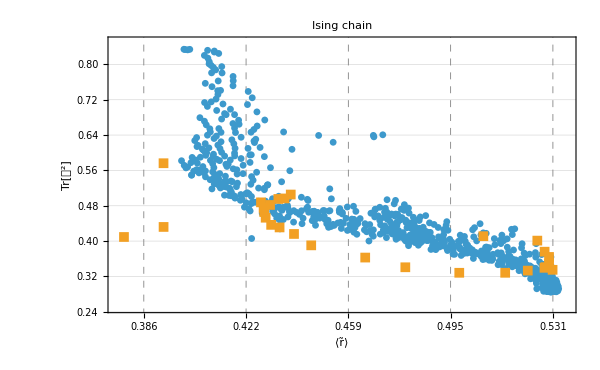

```mathematica
i=1;
figising=ListPlot[{#,#[[28*(i-1)+1;;28*i]]}&[Transpose[{rtilde,meanchoipurity}]],
Joined->{False,False},
PlotRange->{{0.3765,0.536},{0.25,0.85}},
PlotStyle->{Automatic},
PlotMarkers->{{Automatic,7},{Automatic,10}},
Frame->True,
FrameStyle->Directive[Black,FontSize->25],
FrameLabel->{"⟨r̃⟩","Tr[𝒟^2]"},
PlotLabel->Style["Ising chain",Black,FontSize->25],
FrameTicks->{
{Automatic,Automatic},
{Table[{i,NumberForm[i,{Infinity,3}]},{i,Subdivide[0.386,0.531,4]}],Table[{i,None},{i,Subdivide[0.386,0.531,4]}]}
},
ImageSize->600,
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thickness[0.001]]
]
```

## XXZ

Importar eigenenergías y calcular ⟨r̃⟩:

```mathematica
data=Import["data/eigenenergies/xxz/L_18_d_9_k_7_Jz_1_omega_0.csv","CSV"];
{parameters,rtilde}=Transpose[{#[[1;;2]],MeanLevelSpacingRatio[#[[3;;]]]}&/@data];ClearAll[data];
```

Divide::infy: Infinite expression (3.90912×10^-7)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Importar valor esperado de Haar de la pureza de Choi y calcular el promedio temporal:

```mathematica
{t0,tf}={0,49.5};
meanchoipurity=Table[
Module[{hz=i[[1]],J=i[[2]],choipurityinterpolated},
choipurityinterpolated=Interpolation[Import["data/haar_avg_choi_purity/ising/L_7/hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>".csv","CSV"][[2;;]]];
NIntegrate[choipurityinterpolated[t],{t,t0,tf}]/tf
]
,{i,parameters}];
```

```mathematica
haarchoipurity=Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1._d_3_omega_0..csv","CSV"][[2;;]];
```

```mathematica
Select[haarchoipurity,#[[1]]==0.2&]//Length
```

51

```mathematica
Subdivide[0.05,5,29]
```

{0.05,0.22069,0.391379,0.562069,0.732759,0.903448,1.07414,1.24483,1.41552,1.58621,1.7569,1.92759,2.09828,2.26897,2.43966,2.61034,2.78103,2.95172,3.12241,3.2931,3.46379,3.63448,3.80517,3.97586,4.14655,4.31724,4.48793,4.65862,4.82931,5.}

```mathematica
parameters[[1;;30,2]]
```

{0.05,0.22069,0.391379,0.562069,0.732759,0.903448,1.07414,1.24483,1.41552,1.58621,1.7569,1.92759,2.09828,2.26897,2.43966,2.61034,2.78103,2.95172,3.12241,3.2931,3.46379,3.63448,3.80517,3.97586,4.14655,4.31724,4.48793,4.65862,4.82931,5.}